```mathematica
(* Long-range behaviour of Qtilde *)
(* From eq. 31 and 32 in the paper *)
r[y_]=rbar((1+y)/(1-y))^(1/α);
g[y_]=D[r[y],y];
F[y_]=Simplify[g''[y]/(2g[y])-3/4(g'[y]/g[y])^2];
```

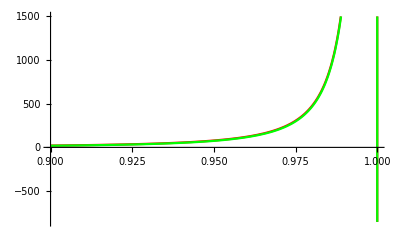

FindRoot::nlnum: The function value {1.87519×10^7-5.00025×10^11 ϵ} is not a list of numbers with dimensions {1} at {y} = {0.9999}.

FindRoot[-(ϵ (1+y)^(2/α-2))/(1-y)^(2/α+2)+(1-1/α^2)/((1-y) (1+y))^2==0,{y,0.9999}]

```mathematica
(* eq. 34 of the paper *)
α=2;
η=0.0001;
Plot[{-η 1/α^2(1+y)^(2/α-2)/(1-y)^(2/α+2)+(1-1/α^2)/((1-y^2)^2),-η 1/α^2(2)^(2/α-2)/(1-y)^(2/α+2)+(1-1/α^2)/(4(1-y)^2)},{y,0.9,1},PlotStyle->{Red,Green}]
FindRoot[-ϵ (1+y)^(2/α-2)/(1-y)^(2/α+2)+(1-1/α^2)/((1-y)(1+y))^2==0,{y,0.9999}]
Clear[α,ϵ,η]
```

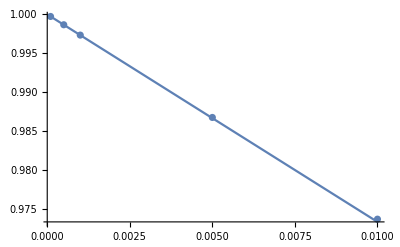

```mathematica
α=2;
(* For α=2, {ϵ, y0}*)
{{0.01,0.9736842105263158},{0.005,0.9867549668874172},{0.001,0.9973368841544618},{0.0005,0.9986675549633578},{0.0001,0.9997333688841488}};
ListPlot[%,PlotRange->All];
Plot[1-((2^(2-2/α) (1/4-1/(4 α^2)))/ϵ)^(-α/2),{ϵ,0.0001,0.01},PlotRange->All];
Show[%,%%,PlotRange->All]
Clear[α]
```

```mathematica
Simplify[Normal[Series[1-((2^(2-2/α) (1/4-1/(4 α^2)))/ϵ)^(-α/2),{α,∞,0}]],ϵ>0]
```

1-2 ⅇ^((1+2 α^2)/(4 α^3)) ϵ^(α/2)

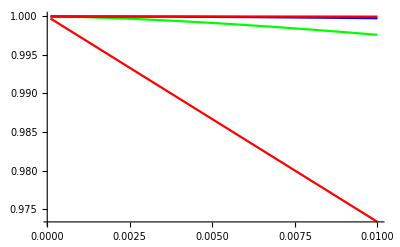

```mathematica
expr=1-2 α^α (-1+α^2)^(-α/2) ϵ^(α/2);
Plot[{expr/.α->2,expr/.α->3,expr/.α->4,(1-2 ⅇ^((1+2 α^2)/(4 α^3)) ϵ^(α/2))/.α->5},{ϵ,0.0001,0.01},PlotRange->All,PlotStyle->{Red,Green,Blue}]
```

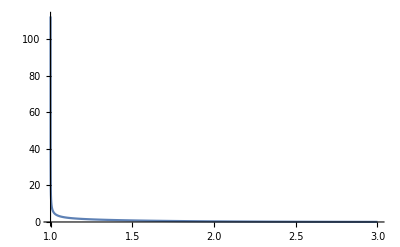

```mathematica
Plot[(-1+α^2)^(-α/2),{α,0,3},PlotRange->All]
```

```mathematica
α=2;η=50;
FindRoot[-η 1/α^2 (1+y)^(2/α-2)/(1-y)^(2/α+2)+(1-1/α^2)/((1-y)(1+y))^2==0,{y,1-2(1/(α^2-1))^(α/2)η^(α/2)}]
1.-2(1/(α^2-1))^(α/2)η^(α/2)
Clear[α,a,b,η]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{y→-1.60972×10^11}

-32.3333

```mathematica
Normal[Series[-η 1/α^2 (1+y)^(2/α-2)/(1-y)^(2/α+2)+(1-1/α^2)/((1-y)(1+y))^2,{α,1,0}]]
```

```mathematica
Solve[-η/(-1+y)^4==0,y]
```

{}

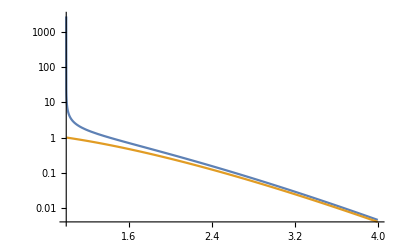

```mathematica
LogPlot[{(1/(α^2-1))^(α/2),α^-α},{α,1,4}]
```

```mathematica
μ=238 0.5*1800;rbar=1.5;ϵ=1/219274;
2μ(2rbar)^2 ϵ
```

17.5835

```mathematica
238 0.5*1800
```

214200.